# Density Plot

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{NotebookDirectory[],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedSteps","ConstrainedInitialSignLeft","ConstrainedInitialSignStepsLeft","ConstrainedInitialSignStepsRight"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"bamboo_1","0001",r,"clean"];

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=150/r;
ny=300/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io}
ImageDimensions[#]&/@{ia,ib,id,io}

max=MinMax[Flatten[ImageData[id]]][[2]];
Print["max dv=", max]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45},{103,45}}

max dv=12.5952

## Test Design

#### Pythagoras

```mathematica
pyth[{x_,y_}]:=Sqrt[(x^2+y^2)]
```

#### RMSE

```mathematica
rmse[x_,y_]:=N@Sqrt[Mean[Power[x-y,2]]]
```

#### Little Functions

```mathematica
pyrfi[ia_,ib_,row_,lvlmax_]:=Block[{pyrfia,pyrfib},
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ib][[row]],lvlmax];

Flatten[{pyrfia,pyrfib},{{2},{1},{3}}]
]
```

#### count colors

```mathematica
(*Counts the amount of colors in solution*)
countColors[v_]:=Block[{count},
count=0;
ImageScan[If[Mean[#]≠0,count++]&,v];
count
]
```

#### N tests

```mathematica
(*Error is updated depending in the highest res level *)
test1[ia_,ib_,lvlmax_,e_,mode_]:=Block[{},(

Table[
stereoDepth[ia,ib,lvlmax,{1,i},e,mode]
,{i,lvlmax}]

)]
```

#### results

```mathematica
res1Display[res1_,id_]:=Block[{maxid,flipMask, signMask, magMask, okMask, convergedMask,imageConverged, imageOk, imageFlip, imageSign, imageMag},(
maxid=MinMax[Flatten[ImageData[id]]][[2]];
npixels=103.*45.;

(*"converged", "ok","oksign","flip","sign","mag"*)
flipMask={"converged"->Transparent,"ok"->Transparent,"oksign"->Transparent,"flip"->Orange,"sign"->Transparent,"mag"->Transparent};
signMask={"converged"->Transparent,"ok"->Transparent,"oksign"->Transparent,"flip"->Transparent,"sign"->Red,"mag"->Transparent};
magMask={"converged"->Transparent,"ok"->Transparent,"oksign"->Transparent,"flip"->Transparent,"sign"->Transparent,"mag"->Purple};
okMask={"converged"->Transparent,"ok"->Pink,"oksign"->Blue,"flip"->Transparent,"sign"->Transparent,"mag"->Transparent};
convergedMask={"converged"->Green,"ok"->Transparent,"oksign"->Transparent,"flip"->Transparent,"sign"->Transparent,"mag"->Transparent};

Table[
imageConverged=Image[res[[All,All,2]]/.convergedMask];
imageOk=Image[res[[All,All,2]]/.okMask];
imageFlip=Image[res[[All,All,2]]/.flipMask];
imageSign=Image[res[[All,All,2]]/.signMask];
imageMag=Image[res[[All,All,2]]/.magMask];

lst1=Flatten[-res[[All,All,1]]];
lst2=Flatten[ImageData[id]];
p=Flatten[Position[Flatten[res[[All,All,2]]],#]&/@{"sign","mag","flip","ok","oksign"},1];
lst11=Delete[lst1,p];
lst22=Delete[lst2,p];

{Image[-res[[All,All,1]]]/(maxid),
id/(maxid),
Grid[{{imageConverged},{countColors[imageConverged]}}],
Grid[{{imageOk},{countColors[imageOk]}}],
Grid[{{imageFlip},{countColors[imageFlip]}}],
Grid[{{imageSign},{countColors[imageSign]}}],
Grid[{{imageMag},{countColors[imageMag]}}],
rmse[lst11,lst22],
rmse[lst1,lst2],
1./countColors[imageConverged]
}
,{res, res1}]
)]
```

#### Display of results

```mathematica
res2ColorCode[result_,id_]:=Block[{},(
minmaxid=MinMax[Flatten[ImageData[id]]];
(*seeStatus={"converged"->Transparent,"ok"->Transparent,"flip"->Red,"sign"->Purple,"mag"->Yellow};*)
flipMask={"converged"->Transparent,"ok"->Transparent,"flip"->Orange,"sign"->Transparent,"oksign"->Transparent,"mag"->Transparent};
signMask={"converged"->Transparent,"ok"->Transparent,"flip"->Transparent,"sign"->Red,"oksign"->Transparent,"mag"->Transparent};
magMask={"converged"->Transparent,"ok"->Transparent,"flip"->Transparent,"sign"->Transparent,"oksign"->Transparent,"mag"->Purple};
okMask={"converged"->Transparent,"ok"->Pink,"flip"->Transparent,"sign"->Transparent,"oksign"->Blue,"mag"->Transparent};
convergedMask={"converged"->Green,"ok"->Transparent,"flip"->Transparent,"sign"->Transparent,"oksign"->Transparent,"mag"->Transparent};

imageConverged=Image[result[[All,All,2]]/.convergedMask];
imageOk=Image[result[[All,All,2]]/.okMask];
imageFlip=Image[result[[All,All,2]]/.flipMask];
imageSign=Image[result[[All,All,2]]/.signMask];
imageMag=Image[result[[All,All,2]]/.magMask];

{Image[-result[[All,All,1]]]/(minmaxid[[2]]),
id/(minmaxid[[2]]),
Grid[{{imageConverged},{countColors[imageConverged]}}],
Grid[{{imageOk},{countColors[imageOk]}}],
Grid[{{imageFlip},{countColors[imageFlip]}}],
Grid[{{imageSign},{countColors[imageSign]}}],
Grid[{{imageMag},{countColors[imageMag]}}]}

)]
```

## Calculating results

```mathematica
e=0.03;
lvls=7;
```

#### Over Constrained {1, n} test

```mathematica
mode="OverConstrained";
```

```mathematica
Subscript[res1, mode]=test1[ia,ib, lvls,e,mode];
```

```mathematica
Subscript[res1Dis, mode]=res1Display[Subscript[res1, mode],id]
```

{{-Graphics-,-Graphics-,-Graphics-
162,-Graphics-
0,-Graphics-
7,-Graphics-
2513,-Graphics-
1953,5.80204,6.65321,0.00617284},{-Graphics-,-Graphics-,-Graphics-
40,-Graphics-
0,-Graphics-
28,-Graphics-
2668,-Graphics-
1899,4.7792,6.64932,0.025},{-Graphics-,-Graphics-,-Graphics-
96,-Graphics-
0,-Graphics-
227,-Graphics-
2604,-Graphics-
1708,1.27876,6.6072,0.0104167},{-Graphics-,-Graphics-,-Graphics-
102,-Graphics-
0,-Graphics-
466,-Graphics-
2052,-Graphics-
2015,1.20551,6.60027,0.00980392},{-Graphics-,-Graphics-,-Graphics-
63,-Graphics-
0,-Graphics-
294,-Graphics-
1643,-Graphics-
2635,1.37188,6.62272,0.015873},{-Graphics-,-Graphics-,-Graphics-
28,-Graphics-
0,-Graphics-
173,-Graphics-
1916,-Graphics-
2518,0.976656,6.63991,0.0357143},{-Graphics-,-Graphics-,-Graphics-
28,-Graphics-
0,-Graphics-
151,-Graphics-
1701,-Graphics-
2755,0.976656,6.63991,0.0357143}}

```mathematica
Subscript[errorRMSE, mode]=Subscript[res1Dis, mode][[All,-3]];
Subscript[density, mode]=Subscript[res1Dis, mode][[All,-1]];
```

```mathematica
Subscript[densityRes, mode]=Flatten[{Subscript[density, mode],Subscript[errorRMSE, mode]},{{2},{1}}];
```

```mathematica
(* Plot values *)
offset={0,0.4};
{maxX,maxY}={Max[Subscript[densityRes, mode][[All,1]]],Max[Subscript[densityRes, mode][[All,2]]]};
```

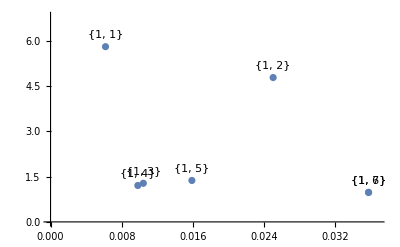

```mathematica
Show[
ListPlot[Subscript[densityRes, mode],PlotRange->{{0,maxX+0.001},{0,maxY+1}}],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
]
```

#### Semi Constrained {1, n} test

```mathematica
mode="SemiConstrained";
```

```mathematica
Subscript[res1, mode]=test1[ia,ib, lvls,e,mode];
```

```mathematica
Subscript[res1Dis, mode]=res1Display[Subscript[res1, mode],id]
```

{{-Graphics-,-Graphics-,-Graphics-
162,-Graphics-
0,-Graphics-
7,-Graphics-
2513,-Graphics-
1953,5.80204,6.66311,0.00617284},{-Graphics-,-Graphics-,-Graphics-
166,-Graphics-
0,-Graphics-
48,-Graphics-
2495,-Graphics-
1926,5.41838,6.55693,0.0060241},{-Graphics-,-Graphics-,-Graphics-
252,-Graphics-
1,-Graphics-
233,-Graphics-
2264,-Graphics-
1885,4.32785,6.26556,0.00396825},{-Graphics-,-Graphics-,-Graphics-
269,-Graphics-
1,-Graphics-
416,-Graphics-
2071,-Graphics-
1878,3.76411,5.75755,0.00371747},{-Graphics-,-Graphics-,-Graphics-
262,-Graphics-
1,-Graphics-
507,-Graphics-
1978,-Graphics-
1887,3.47343,5.55802,0.00381679},{-Graphics-,-Graphics-,-Graphics-
240,-Graphics-
1,-Graphics-
601,-Graphics-
1931,-Graphics-
1862,3.16173,6.14713,0.00416667},{-Graphics-,-Graphics-,-Graphics-
206,-Graphics-
2,-Graphics-
613,-Graphics-
1987,-Graphics-
1827,4.5565,14.2248,0.00485437}}

```mathematica
Subscript[errorRMSE, mode]=Subscript[res1Dis, mode][[All,-3]];
Subscript[density, mode]=Subscript[res1Dis, mode][[All,-1]];
```

```mathematica
Subscript[densityRes, mode]=Flatten[{Subscript[density, mode],Subscript[errorRMSE, mode]},{{2},{1}}];
```

```mathematica
(* Plot values *)
offset={0,0.4};
{maxX,maxY}={Max[Subscript[densityRes, mode][[All,1]]],Max[Subscript[densityRes, mode][[All,2]]]};
```

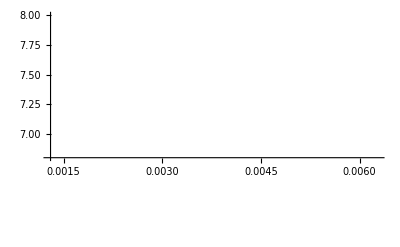

```mathematica
Show[
ListPlot[Subscript[densityRes, mode],PlotRange->{{0.0013,maxX+0.0001},{8,maxY+1}}],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
]
```

#### Constrained {1, n} test

```mathematica
mode="Constrained";
```

```mathematica
Subscript[res1, mode]=test1[ia,ib, lvls,e,mode];
```

```mathematica
Subscript[res1Dis, mode]=res1Display[Subscript[res1, mode],id]
```

{{-Graphics-,-Graphics-,-Graphics-
162,-Graphics-
0,-Graphics-
7,-Graphics-
2513,-Graphics-
1953,5.80204,6.66311,0.00617284},{-Graphics-,-Graphics-,-Graphics-
166,-Graphics-
0,-Graphics-
48,-Graphics-
2495,-Graphics-
1926,5.41838,6.62342,0.0060241},{-Graphics-,-Graphics-,-Graphics-
136,-Graphics-
1,-Graphics-
211,-Graphics-
2590,-Graphics-
1697,2.67063,6.48852,0.00735294},{-Graphics-,-Graphics-,-Graphics-
150,-Graphics-
0,-Graphics-
395,-Graphics-
2560,-Graphics-
1530,1.37086,6.45673,0.00666667},{-Graphics-,-Graphics-,-Graphics-
132,-Graphics-
0,-Graphics-
514,-Graphics-
2112,-Graphics-
1877,1.3327,6.52165,0.00757576},{-Graphics-,-Graphics-,-Graphics-
83,-Graphics-
0,-Graphics-
380,-Graphics-
1752,-Graphics-
2420,1.51122,6.57454,0.0120482},{-Graphics-,-Graphics-,-Graphics-
55,-Graphics-
0,-Graphics-
243,-Graphics-
2320,-Graphics-
2017,0.865656,6.59079,0.0181818}}

```mathematica
Subscript[errorRMSE, mode]=Subscript[res1Dis, mode][[All,-3]];
Subscript[density, mode]=Subscript[res1Dis, mode][[All,-1]];
```

```mathematica
Subscript[densityRes, mode]=Flatten[{Subscript[density, mode],Subscript[errorRMSE, mode]},{{2},{1}}];
```

```mathematica
(* Plot values *)
offset={0,0.4};
{maxX,maxY}={Max[Subscript[densityRes, mode][[All,1]]],Max[Subscript[densityRes, mode][[All,2]]]};
```

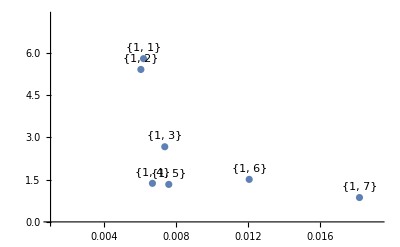

```mathematica
Show[
ListPlot[Subscript[densityRes, mode],PlotRange->{{0.001,maxX+0.001},{0,maxY+1.5}}],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
]
```

#### Constrained Smaller Steps {1, n} and e=e/4 test

```mathematica
mode="ConstrainedSteps";
```

```mathematica
Subscript[res1, mode]=test1[ia,ib, lvls,e/4,mode];
```

```mathematica
Subscript[res1Dis, mode]=res1Display[Subscript[res1, mode],id]
```

{{-Graphics-,-Graphics-,-Graphics-
538,-Graphics-
38,-Graphics-
13,-Graphics-
2937,-Graphics-
1109,5.5726,6.55612,0.00185874},{-Graphics-,-Graphics-,-Graphics-
641,-Graphics-
25,-Graphics-
395,-Graphics-
2708,-Graphics-
866,4.89078,6.382,0.00156006},{-Graphics-,-Graphics-,-Graphics-
492,-Graphics-
1,-Graphics-
817,-Graphics-
2622,-Graphics-
703,2.81197,6.06625,0.00203252},{-Graphics-,-Graphics-,-Graphics-
412,-Graphics-
0,-Graphics-
1245,-Graphics-
2352,-Graphics-
626,1.95845,6.14966,0.00242718},{-Graphics-,-Graphics-,-Graphics-
337,-Graphics-
0,-Graphics-
1476,-Graphics-
2160,-Graphics-
662,1.72316,6.27716,0.00296736},{-Graphics-,-Graphics-,-Graphics-
246,-Graphics-
0,-Graphics-
1305,-Graphics-
2203,-Graphics-
881,1.77558,6.40854,0.00406504},{-Graphics-,-Graphics-,-Graphics-
184,-Graphics-
0,-Graphics-
916,-Graphics-
2807,-Graphics-
728,1.70847,6.45926,0.00543478}}

```mathematica
Subscript[errorRMSE, mode]=Subscript[res1Dis, mode][[All,-3]];
Subscript[density, mode]=Subscript[res1Dis, mode][[All,-1]];
```

```mathematica
Subscript[densityRes, mode]=Flatten[{Subscript[density, mode],Subscript[errorRMSE, mode]},{{2},{1}}];
```

```mathematica
(* Plot values *)
offset={0,0.4};
{maxX,maxY}={Max[Subscript[densityRes, mode][[All,1]]],Max[Subscript[densityRes, mode][[All,2]]]};
```

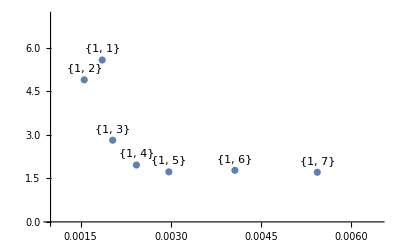

```mathematica
Show[
ListPlot[Subscript[densityRes, mode],PlotRange->{{0.001,maxX+0.001},{0,maxY+1.5}}],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
]
```

#### Constrained Initial Sign Left {1, n} test

```mathematica
mode="ConstrainedInitialSignLeft";
```

```mathematica
Subscript[res1, mode]=test1[ia,ib, lvls,e,mode];
```

```mathematica
Subscript[res1Dis, mode]=res1Display[Subscript[res1, mode],id]
```

{{-Graphics-,-Graphics-,-Graphics-
182,-Graphics-
0,-Graphics-
138,-Graphics-
296,-Graphics-
4019,5.69432,6.72698,0.00549451},{-Graphics-,-Graphics-,-Graphics-
189,-Graphics-
0,-Graphics-
231,-Graphics-
275,-Graphics-
3940,5.23384,6.64802,0.00529101},{-Graphics-,-Graphics-,-Graphics-
151,-Graphics-
1,-Graphics-
354,-Graphics-
419,-Graphics-
3710,2.57809,6.19899,0.00662252},{-Graphics-,-Graphics-,-Graphics-
158,-Graphics-
0,-Graphics-
514,-Graphics-
702,-Graphics-
3261,1.41445,6.12119,0.00632911},{-Graphics-,-Graphics-,-Graphics-
132,-Graphics-
0,-Graphics-
596,-Graphics-
469,-Graphics-
3438,1.3327,6.28928,0.00757576},{-Graphics-,-Graphics-,-Graphics-
83,-Graphics-
0,-Graphics-
444,-Graphics-
274,-Graphics-
3834,1.51122,6.43361,0.0120482},{-Graphics-,-Graphics-,-Graphics-
55,-Graphics-
0,-Graphics-
320,-Graphics-
359,-Graphics-
3901,0.865656,6.47683,0.0181818}}

```mathematica
Subscript[errorRMSE, mode]=Subscript[res1Dis, mode][[All,-3]];
Subscript[density, mode]=Subscript[res1Dis, mode][[All,-1]];
```

```mathematica
Subscript[densityRes, mode]=Flatten[{Subscript[density, mode],Subscript[errorRMSE, mode]},{{2},{1}}];
```

```mathematica
(* Plot values *)
offset={0,0.4};
{maxX,maxY}={Max[Subscript[densityRes, mode][[All,1]]],Max[Subscript[densityRes, mode][[All,2]]]};
```

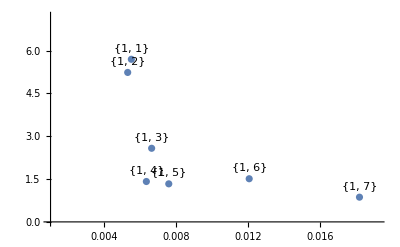

```mathematica
Show[
ListPlot[Subscript[densityRes, mode],PlotRange->{{0.001,maxX+0.001},{0,maxY+1.5}}],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
]
```

#### Constrained Initial Sign Right {1, n} and e=e/4 test

```mathematica
mode="ConstrainedInitialSignStepsRight";
```

```mathematica
Subscript[res1, mode]=test1[ia,ib, lvls,e/4,mode];
```

```mathematica
Subscript[res1Dis, mode]=res1Display[Subscript[res1, mode],id]
```

{{-Graphics-,-Graphics-,-Graphics-
621,-Graphics-
49,-Graphics-
654,-Graphics-
921,-Graphics-
2390,5.68584,7.09006,0.00161031},{-Graphics-,-Graphics-,-Graphics-
700,-Graphics-
29,-Graphics-
1337,-Graphics-
760,-Graphics-
1809,5.49251,8.10373,0.00142857},{-Graphics-,-Graphics-,-Graphics-
528,-Graphics-
1,-Graphics-
1492,-Graphics-
1039,-Graphics-
1575,4.53526,6.06225,0.00189394},{-Graphics-,-Graphics-,-Graphics-
430,-Graphics-
0,-Graphics-
1872,-Graphics-
1066,-Graphics-
1267,4.59897,5.98677,0.00232558},{-Graphics-,-Graphics-,-Graphics-
338,-Graphics-
0,-Graphics-
2112,-Graphics-
872,-Graphics-
1313,2.99014,6.00443,0.00295858},{-Graphics-,-Graphics-,-Graphics-
247,-Graphics-
0,-Graphics-
1918,-Graphics-
830,-Graphics-
1640,2.98469,6.31587,0.00404858},{-Graphics-,-Graphics-,-Graphics-
184,-Graphics-
0,-Graphics-
1860,-Graphics-
1163,-Graphics-
1428,2.99312,6.39069,0.00543478}}

```mathematica
Subscript[errorRMSE, mode]=Subscript[res1Dis, mode][[All,-3]];
Subscript[density, mode]=Subscript[res1Dis, mode][[All,-1]];
```

```mathematica
Subscript[densityRes, mode]=Flatten[{Subscript[density, mode],Subscript[errorRMSE, mode]},{{2},{1}}];
```

```mathematica
(* Plot values *)
offset={0,0.4};
{maxX,maxY}={Max[Subscript[densityRes, mode][[All,1]]],Max[Subscript[densityRes, mode][[All,2]]]};
```

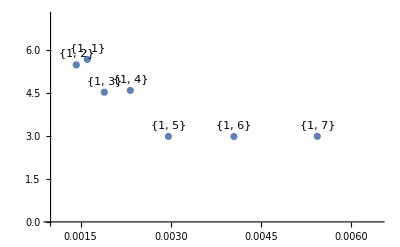

```mathematica
Show[
ListPlot[Subscript[densityRes, mode],PlotRange->{{0.001,maxX+0.001},{0,maxY+1.5}}],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
]
```

#### Constrained Initial Sign Left {1, n} and e=e/4 test

```mathematica
mode="ConstrainedInitialSignStepsLeft";
```

```mathematica
Subscript[res1, mode]=test1[ia,ib, lvls,e/4,mode];
```

```mathematica
Subscript[res1Dis, mode]=res1Display[Subscript[res1, mode],id]
```

{{-Graphics-,-Graphics-,-Graphics-
658,-Graphics-
51,-Graphics-
657,-Graphics-
924,-Graphics-
2345,5.945,7.03925,0.00151976},{-Graphics-,-Graphics-,-Graphics-
740,-Graphics-
31,-Graphics-
1337,-Graphics-
752,-Graphics-
1775,5.11964,7.60038,0.00135135},{-Graphics-,-Graphics-,-Graphics-
534,-Graphics-
5,-Graphics-
1581,-Graphics-
999,-Graphics-
1516,3.74523,5.78141,0.00187266},{-Graphics-,-Graphics-,-Graphics-
441,-Graphics-
1,-Graphics-
1889,-Graphics-
1003,-Graphics-
1301,2.9453,5.57883,0.00226757},{-Graphics-,-Graphics-,-Graphics-
345,-Graphics-
0,-Graphics-
2100,-Graphics-
886,-Graphics-
1304,2.61328,5.92927,0.00289855},{-Graphics-,-Graphics-,-Graphics-
246,-Graphics-
0,-Graphics-
1903,-Graphics-
855,-Graphics-
1631,7.36347,6.75617,0.00406504},{-Graphics-,-Graphics-,-Graphics-
184,-Graphics-
0,-Graphics-
1865,-Graphics-
1138,-Graphics-
1448,2.19881,6.32904,0.00543478}}

```mathematica
Subscript[errorRMSE, mode]=Subscript[res1Dis, mode][[All,-3]];
Subscript[density, mode]=Subscript[res1Dis, mode][[All,-1]];
```

```mathematica
Subscript[densityRes, mode]=Flatten[{Subscript[density, mode],Subscript[errorRMSE, mode]},{{2},{1}}];
```

```mathematica
(* Plot values *)
offset={0,0.4};
{maxX,maxY}={Max[Subscript[densityRes, mode][[All,1]]],Max[Subscript[densityRes, mode][[All,2]]]};
```

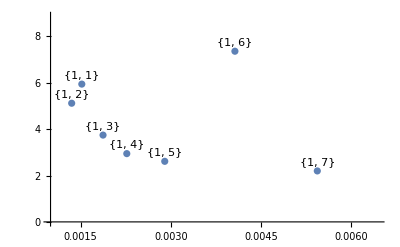

```mathematica
Show[
ListPlot[Subscript[densityRes, mode],PlotRange->{{0.001,maxX+0.001},{0,maxY+1.5}}],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
]
```

#### All {1, n} test

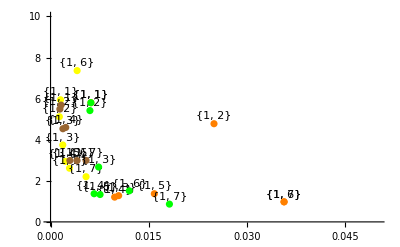

```mathematica
(* Closest Value to {0,0} wins *)
rangexyPlot={{0,0.05},{0,10}};
Show[{
mode="OverConstrained";
ListPlot[Subscript[densityRes, mode],PlotRange->rangexyPlot,PlotStyle->Orange],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}],
(*mode="SemiConstrained";
ListPlot[Subscript[densityRes, mode],PlotRange->rangexyPlot,PlotStyle->Red],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}],*)
mode="Constrained";
ListPlot[Subscript[densityRes, mode],PlotRange->rangexyPlot,PlotStyle->Green],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}],
(*mode="ConstrainedSteps";
ListPlot[Subscript[densityRes, mode],PlotRange->rangexyPlot,PlotStyle->Purple],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}],*)
(*mode="ConstrainedInitialSign";
ListPlot[Subscript[densityRes, mode],PlotRange->rangexyPlot,PlotStyle->Blue],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}],*)
mode="ConstrainedInitialSignStepsLeft";
ListPlot[Subscript[densityRes, mode],PlotRange->rangexyPlot,PlotStyle->Yellow],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}],
mode="ConstrainedInitialSignStepsRight";
ListPlot[Subscript[densityRes, mode],PlotRange->rangexyPlot,PlotStyle->Brown],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
},ImageSize->Scaled[0.5]]
```

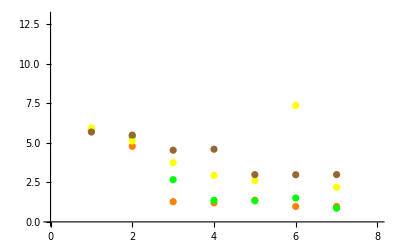

```mathematica
(* Smallest value Wins *)
Show[{
mode="OverConstrained";
ListPlot[pyth[#]&/@Subscript[densityRes, mode],PlotStyle->Orange,PlotRange->{{0,lvls+1},{0,13}}],
(*mode="SemiConstrained";
ListPlot[pyth[#]&/@Subscript[densityRes, mode],PlotStyle->Red],*)
mode="Constrained";
ListPlot[pyth[#]&/@Subscript[densityRes, mode],PlotStyle->Green],
(*mode="ConstrainedSteps";
ListPlot[pyth[#]&/@Subscript[densityRes, mode],PlotStyle->Purple],
mode="ConstrainedInitialSign";
ListPlot[pyth[#]&/@Subscript[densityRes, mode],PlotStyle->Blue],*)
mode="ConstrainedInitialSignStepsLeft";
ListPlot[pyth[#]&/@Subscript[densityRes, mode],PlotStyle->Yellow],
mode="ConstrainedInitialSignStepsRight";
ListPlot[pyth[#]&/@Subscript[densityRes, mode],PlotStyle->Brown]
},
ImageSize->Scaled[0.5]]
```